# Two-Flavor Matter effects

0.693437

{{En→0.00110082}}

0.00110082

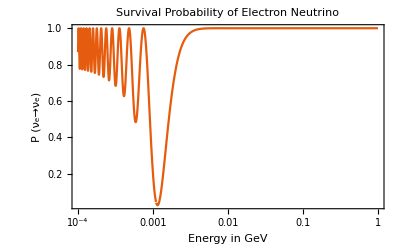

```mathematica
L=30 * 5 *10^18;                                                                (*(GeV)^-1*)    
delta= 3*10^-23;                                                              (*(GeV)^2*)                                       
rh[r_]:=160*4.36*10^-18*Exp[-r];                   (*(GeV)^4*)                                                                
theta= ArcSin[Sqrt[0.05]]   ;      
                                                                                                                                                                                               
A[En_]:=2*Sqrt[2]*1.166*10^-5*1/0.938*rh[0]*En;                                                                     
deltaM[En_]:=((A[En]-delta* Cos[2*theta])^2+(delta*Sin[2*theta])^2 )^(0.5) ;                                                                                                                                                         
thetam[En_]:=0.5* ArcTan[(delta*Sin[2 *theta])/Abs[(A[En]-delta*Cos[2*theta])]];                               
thetam[0.0012]

Simplify@Solve[FullSimplify[A[En]-delta*Cos[2*theta]]==0,{En}]                      (*ANS------2*)
Ea=0.001100820697938                                                                                                                              (*ANS------3*)

Pmee[En_]:= 1- Sin[2*thetam[En]]^2*Sin[ deltaM[En]*L/En]^2  ;          
LogLinearPlot[Pmee[En], {En,10^-4,1}, PlotRange->All, PlotTheme-> "Scientific", FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, e])],None},{HoldForm[Energy in GeV],None}},PlotLabel->HoldForm[Survival Probability of Electron Neutrino]]
```